#### Kirill Zakharov Pade Approximation

```mathematica
Clear[padeApprox]
```

```mathematica
funD[fun_,y_,k_,h_]:=D[fun[y],{y,k}]/.y-> h
```

```mathematica
padeApprox[fun_,x0_,m_]:=Module[{t,x=x0,array={}},Do[t=(-fun[x])/funD[k,i,x];x=x^2/(x-t);AppendTo[array,x],{i,1,m}];N/@array]
```

#### Задаем функцию

```mathematica
fun[y_]:=y^3+6 y^2+9y-4
```

```mathematica
lst=padeApprox[fun,3.6,3];
```

#### Ответ

```mathematica
lst⟦3⟧
```

0.354205

#### Визуальное представление

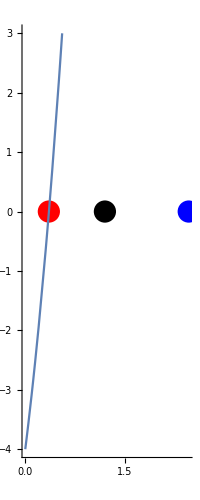

```mathematica
Show[Graphics[{PointSize[0.04],Blue,Point[{lst⟦1⟧,0}],Black,Point[{lst⟦2⟧,0}],Red,Point[{lst⟦3⟧,0}]},Axes->True],Plot[x^3+6 x^2+9x-4,{x,-5,5},PlotRange->{Automatic,{-4,3}}]]
```

#### Проверка

```mathematica
Solve[x^3+6 x^2+9x-4==0,x]
```

{{x→Root0.355Root[-4+9 #1+6 #1^2+#1^3&,1]0.3553013976081199},{x→Root-3.18-1.08 ⅈRoot[-4+9 #1+6 #1^2+#1^3&,2]-3.1776506988040603},{x→Root-3.18+1.08 ⅈRoot[-4+9 #1+6 #1^2+#1^3&,3]-3.1776506988040603}}